# Въведение

```mathematica
6 + 7
```

```mathematica
13
```

Пояснение за работа със списъци:

```mathematica
vec = {4,5,{1/2, 5^2},ⅇ, ArcSin[23.89]}
```

{4,5,{1/2,25},ⅇ,1.5708-3.86617 ⅈ}

```mathematica
vec1 = {4,5,{1/2, 5^2},ⅇ, ArcSin[23.89]};
vec1
```

{4,5,{1/2,25},ⅇ,1.5708-3.86617 ⅈ}

```mathematica
vec^2
```

{16,25,{1/4,625},ⅇ^2,-12.4799-12.1459 ⅈ}

```mathematica
Tan[vec]
```

{Tan[4],Tan[5],{Tan[1/2],Tan[25]},Tan[ⅇ],1.07476×10^-19-1.00088 ⅈ}

```mathematica
%//N
```

{1.15782,-3.38052,{0.546302,-0.133526},-0.45055,1.07476×10^-19-1.00088 ⅈ}

```mathematica
vec2 = {4.0,5.,{1./2, 5.^2},ⅇ//N, ArcSin[23.89]};
Tan[vec2]
```

{1.15782,-3.38052,{0.546302,-0.133526},-0.45055,1.07476×10^-19-1.00088 ⅈ}

Начин за изписване на функции

```mathematica
1.1578212823495777
```

```mathematica
Tan@vec2
```

{1.15782,-3.38052,{0.546302,-0.133526},-0.45055,1.07476×10^-19-1.00088 ⅈ}

```mathematica
vec2//Tan
```

{1.15782,-3.38052,{0.546302,-0.133526},-0.45055,1.07476×10^-19-1.00088 ⅈ}

```mathematica
N[ⅇ]
```

2.71828

```mathematica
N[ⅇ, 20]
```

2.7182818284590452354

```mathematica
N[ⅇ, 200] (* Неперовото число с 200 значещи цифри *)
```

2.718281828459045235360287471352662497757247093699959574966967627724076630353547594571382178525166427427466391932003059921817413596629043572900334295260595630738132328627943490763233829880753195251019

# КЧМ за решаване на нелинейни уравнения

Задача: Дадено е уравенението:
x^5 + 103 sin x  - 34 x^3 - 23 = 0
1. Да се визуализира функцията и да се определят броя на корените.
2. Да се локализира един от корените.
3. Уточнете локализирания корен.
4. Оценка на грешката.

```mathematica
f[x_]:=  x^5+103 Sin[x]-34 x^3-23
```

```mathematica
f[x]
```

-23-34 x^3+x^5+103 Sin[x]

## 1. Да се визуализира функцията и да се определят броя на корените.

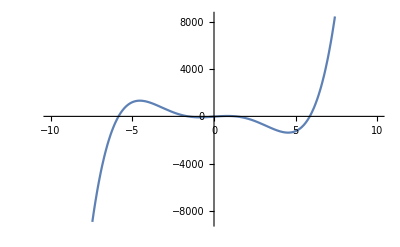

```mathematica
Plot[f[x],{x,-10,10}]
```

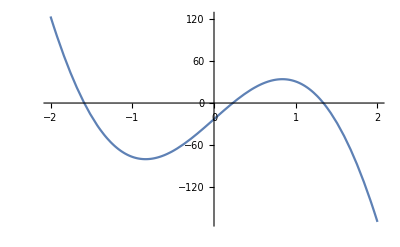

```mathematica
Plot[f[x],{x,-2,2}]
```

## 2. Да се локализира един от корените.

Локализираме най-малкия корен

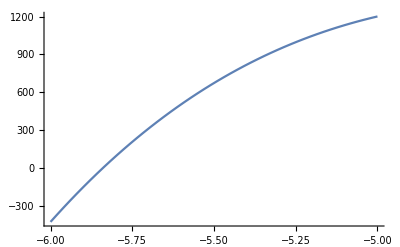

```mathematica
Plot[f[x],{x,-6,-5}]
```

```mathematica
f[-6.]
```

-426.22

```mathematica
f[-5.]
```

1200.77

Извод:
(1) Функцията е непрекъсната, защото е сума от непрекъснати функции (полином и синус)
(2) f(-6) = -426.22... < 0
       f(-5) = 1200.77... > 0
       => Функцията има различни знаци в двата края на разглеждания интервал [-6; -5].
       От (1) и (2) следва, че функцията има поне един корен в разглеждания интервал [-6; -5].

## 3. Уточнете локализирания корен.

## 4. Оценка на грешката.